# Wind Turbine Designer Tool

## Math Model

### Constants

#### Air Density (δa)

```mathematica
δa=1.225;
```

```mathematica
CPmax = 0.5925925925925926;
```

### Equations

#### Wind Power

```mathematica
Pw[Vw_, R_, CP_]:= 1/2 CP δa Vw^3 R^2 π;
```

#### Rotor radius

```mathematica
RotorRadius[Po_,  Vw_, Cp_]:=√((2*Po)/(δa * Vw^3*Cp * π));
```

#### Tip Speed Ratio (λ)

```mathematica
TSR[Vw_, rpm_, R_]:= R*rpm*π / (Vw * 30);
```

#### Revolutions Per Minutes

```mathematica
RPM[Vw_, λ_,  R_]:= (λ * 30 * Vw)/(R*π);
```

```mathematica
RPM2[Vw_, rpmmax_,λ_,R_]:= Piecewise[{{RPM[Vw,λ, R], RPM[Vw,λ, R] ≤rpmmax  }, {rpmmax,  RPM[Vw,λ, R]>rpmmax}}]
```

#### Average Chord Length

```mathematica
AverageChordLength[R_,Sp_,Cl_,Z_]:=(R * Sp)/(Cl * Z);
```

#### Chord Length List

```mathematica
ChordLength[R_, Vw_, Z_, Cl_, λ_, Vr_]:=(2 π R 8 Vw)/(Z 9 Cl λ Vr);
```

#### Solidity

```mathematica
Solidity[R_,l_,Z_]:=(Z*l)/(π*R);
```

#### Blade Velocity

```mathematica
Vu[ R_, rpm_]:=R*rpm*π/30;
```

#### Relative Wind Velocity

```mathematica
Vr[Vw_, Vu_]:=√((2/3 Vw)^2+ Vu^2);
```

#### Wind Angle (θ)

```mathematica
theta[λr_]:=ArcTan[2/(3 λr)]/ Degree;
```

#### Forces on the Blade

```mathematica
Fblade[CFT_, Vr_, L_, dr_]:=1/2 CFT δa Vr^2 L dr;
```

## Airfoil Data

### Airfoil Specifications: A18

#### Aerodynamic Data

```mathematica
A18AlphaData=List[-9.25,-9.0,-8.75,-8.5,-8.25,-8.0,-7.75,-7.5,-7.25,-7.0,-6.75,-6.5,-6.25,-6.0,-5.75,-5.5,-5.25,-5.0,-4.75,-4.5,-4.25,-4.0,-3.75,-3.5,-3.25,-3.0,-2.75,-2.5,-2.25,-2.0,-1.75,-1.5,-1.25,-1.0,-0.75,-0.5,-0.25,0.0,0.25,0.5,0.75,1.0,1.25,1.5,1.75,2.0,2.25,2.5,2.75,3.0,3.25,3.5,3.75,4.0,4.25,4.5,4.75,5.0,5.25,5.5,5.75,6.0,6.25,6.5,6.75,7.0,7.25,7.5,7.75,8.0,8.25,8.5,8.75,9.0,9.25,9.5,9.75,10.0,10.25,10.5,10.75,11.0,11.25,11.5,11.75,12.0,12.25];
A18CLData=List[-0.4152,-0.4198,-0.4263,-0.4291,-0.4307,-0.4302,-0.4264,-0.414,-0.3984,-0.3732,-0.3239,-0.3032,-0.2712,-0.249,-0.2208,-0.1945,-0.1688,-0.1367,-0.0972,-0.0597,-0.0211,0.0151,0.0529,0.0883,0.1259,0.1605,0.1967,0.2324,0.2663,0.3047,0.3362,0.3732,0.4014,0.4255,0.4599,0.4909,0.5229,0.5555,0.5872,0.6172,0.6473,0.6773,0.7071,0.7352,0.7638,0.7912,0.8185,0.8454,0.8718,0.8977,0.9233,0.9484,0.9726,0.9954,1.0168,1.0359,1.0492,1.0649,1.0841,1.1005,1.1157,1.1326,1.1492,1.1656,1.1803,1.1938,1.2102,1.2263,1.2432,1.2603,1.2757,1.2876,1.2958,1.3,1.2991,1.2922,1.282,1.2694,1.2548,1.239,1.2217,1.2039,1.1856,1.1661,1.1459,1.123,1.0913];
A18CDData=List[0.09313,0.08991,0.08677,0.08301,0.07885,0.07409,0.06779,0.05704,0.05493,0.04704,0.03067,0.03073,0.02698,0.02664,0.02517,0.02368,0.02283,0.02195,0.0208,0.01986,0.01917,0.01858,0.01808,0.01764,0.01717,0.01677,0.01639,0.01607,0.01581,0.01544,0.01519,0.0147,0.01416,0.0133,0.01327,0.01328,0.01326,0.01324,0.01323,0.01326,0.0133,0.01331,0.01332,0.01337,0.01344,0.01357,0.01373,0.01391,0.01412,0.01436,0.01462,0.01492,0.0153,0.01577,0.01629,0.01712,0.01861,0.0201,0.02118,0.0226,0.02423,0.02563,0.02699,0.02837,0.02992,0.03172,0.03332,0.03526,0.03745,0.03989,0.04248,0.04497,0.04748,0.05036,0.05378,0.05717,0.06065,0.06432,0.06827,0.07252,0.07726,0.08248,0.08831,0.09501,0.10279,0.11244,0.12734];
```

#### Lift Coefficient (CL) in function of attact angle (α)

```mathematica
A18FCL = Interpolation[Thread[{A18AlphaData, A18CLData}]];
```

#### Drag Coefficient (CD) in function of attact angle (α)

```mathematica
A18FCD= Interpolation[Thread[{A18AlphaData, A18CDData}]];
```

#### Plotting Functions

```mathematica
Show[ Plot[{Labeled[A18FCL[α],"CL"], Labeled[A18FCD[α],"CD"]},{α, -9.5, 12.5}, AxesLabel->{"Angel α","Coefficient"}]]
```

InterpolatingFunction::dmval: Input value {-9.49955} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

#### Airfoil Geometry

```mathematica
A18Geometry = List[{1.00000000,0.00614000},{0.94999999,0.01817000},{0.89999998,0.02858000},{0.80000001,0.04624000},{0.69999999,0.06056000},{0.60000002,0.07197000},{0.55000001,0.07612000},{0.50000000,0.07975000},{0.44999999,0.08293000},{0.40000001,0.08376000},{0.34999999,0.08466000},{0.30000001,0.08383000},{0.25000000,0.08065000},{0.20000000,0.07601000},{0.15000001,0.07026000},{0.10000000,0.06234000},{0.07500000,0.05660000},{0.05000000,0.04923000},{0.02500000,0.03947000},{0.01250000,0.03239000},{0.00000000,0.01865000},{0.01250000,0.00781000},{0.02500000,0.00357000},{0.05000000,0.00075000},{0.07500000,0.00000000},{0.10000000,0.00006000},{0.15000001,0.00200000},{0.20000000,0.00475000},{0.25000000,0.00806000},{0.30000001,0.01038000},{0.34999999,0.01353000},{0.40000001,0.01657000},{0.44999999,0.01780000},{0.50000000,0.01884000},{0.55000001,0.01980000},{0.60000002,0.01998000},{0.69999999,0.01924000},{0.80000001,0.01452000},{0.89999998,0.00813000},{0.94999999,0.00434000},{1.00000000,0.00000000}];
```

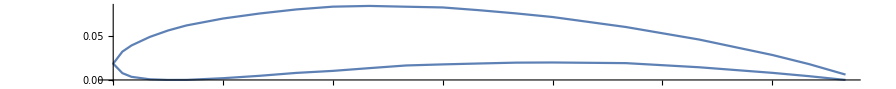

```mathematica
ListLinePlot[A18Geometry, AspectRatio->.1]
```

## Designer

### Design Parameters

#### Air Velocity

```mathematica
Vw = 10;
```

#### Proposed RPM

```mathematica
rpm1 =200;
```

#### Number of Blades

```mathematica
Z1 = 3;
```

#### Number of Ribs (Blade Sections)

```mathematica
Nr = 20;
```

#### Design Power

```mathematica
Pd = 5000;
```

### Common Calculations

#### Calculate the rotor radius

```mathematica
R1 = Round[RotorRadius[Pd, Vw , .40], .01]
```

2.55

#### Calculate the “Tip Speed Ratio” (λ)

```mathematica
λd = TSR[Vw, rpm1, R1]
```

5.34071

```mathematica
TSRD[V_]:= Piecewise[{{λd,RPM[V,λd, R1] ≤ rpm1},{ TSR[V, rpm1, R1],RPM[V,λd, R1] > rpm1}}];
```

#### Differential of the radius (Δr)

```mathematica
Δr =(R1 - 0.10*R1) / (Nr -1)
```

0.120789

#### Vector of ribs radius

```mathematica
Rb = Table[x,{x,R1 - Δr*(Nr-1),  R1,Δr  }]
```

{0.255,0.375789,0.496579,0.617368,0.738158,0.858947,0.979737,1.10053,1.22132,1.34211,1.46289,1.58368,1.70447,1.82526,1.94605,2.06684,2.18763,2.30842,2.42921,2.55}

#### Calculating the blade velocity list

```mathematica
Vus1 =Vu[Rb, rpm1]
```

{5.34071,7.87052,10.4003,12.9301,15.4599,17.9898,20.5196,23.0494,25.5792,28.109,30.6388,33.1686,35.6984,38.2282,40.758,43.2878,45.8176,48.3475,50.8773,53.4071}

#### Calculating the relative wind velocity list

```mathematica
Vrs1 = Vr[Vw ,Vus1]
```

{8.54211,10.3145,12.3536,14.5476,16.8361,19.1853,21.5754,23.9941,26.4337,28.8887,31.3557,33.8319,36.3156,38.8052,41.2997,43.7982,46.3001,48.8049,51.3122,53.8216}

#### Calculating the speed ratio list

```mathematica
λr1  = λd *Rb /R1
```

{0.534071,0.787052,1.04003,1.29301,1.54599,1.79898,2.05196,2.30494,2.55792,2.8109,3.06388,3.31686,3.56984,3.82282,4.0758,4.32878,4.58176,4.83475,5.08773,5.34071}

#### Calculating the relative air angle

```mathematica
θs1 = theta[λr1]
```

{51.3016,40.266,32.6601,27.2752,23.3268,20.3338,17.9986,16.1317,14.6079,13.3424,12.2756,11.3646,10.5781,9.8924,9.28943,8.75521,8.27869,7.85105,7.46518,7.11528}

#### Common Parameters

```mathematica
getMaxValue1[function_]:=FindMaximum[{function, α ≥ αlim2 && α ≤ αlim1},{α,αlim2+(αlim1 -αlim2 )/2}][[1]];
```

```mathematica
getMaxValue2[function_]:=α/. FindMaximum[{function, α ≥ αlim2 && α ≤ αlim1},{α,αlim2+(αlim1 -αlim2 )/2}][[2]];
```

### Airfoil A18

#### “Tangential Force Coefficient” (CFT) and “Normal Force Coefficient “(CFN) in function of attack angle “α” and the speed ratio “λ”

```mathematica
A18CFT[α_, λ_]:= A18FCL[α]* Sin[theta[λ] Degree] - A18FCD[α]* Cos[theta[λ] Degree]
A18CFN[α_, λ_]:=  A18FCL[α]* Cos[theta[λ] Degree] + A18FCD[α]* Sin[theta[λ] Degree]
```

```mathematica
Plot3D[{A18CFT[α,λ], A18CFN[α,λ]},{α,-9,12},{λ,0,λd}]
```

-Graphics3D-

#### Max attact angle

```mathematica
αlim1 = 14;
αlim2 = -8;
```

```mathematica
A18MaxAngle=α/. FindMaximum[{A18FCL[α], α ≥αlim2 && α ≤αlim1},{α,αlim2+(αlim1 -αlim2 )/2}][[2]]
```

InterpolatingFunction::dmval: Input value {13.8906} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

9.08565

#### Calculating the chord length

```mathematica
A18Length= AverageChordLength[R1, .3,A18FCL[A18MaxAngle], Z1]
```

0.196107

#### Calculating the solidity

```mathematica
A18Solidity = Solidity[R1,A18Length,Z1]
```

0.0734385

#### Calculating the maximum CL for speed ratio

```mathematica
A18MaxCFT = Map[getMaxValue1,A18CFT[α,λr1]]
```

InterpolatingFunction::dmval: Input value {13.969} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{0.983127,0.80201,0.65959,0.551689,0.469506,0.405781,0.355347,0.314651,0.281238,0.253388,0.22987,0.209774,0.192431,0.177336,0.164099,0.152409,0.142013,0.132727,0.124401,0.116909}

#### Calculating the angle for the maximum CL for speed ratio

```mathematica
A18MaxAlpha = Map[getMaxValue2,A18CFT[α,λr1]]
```

InterpolatingFunction::dmval: Input value {13.969} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{8.96942,8.91611,8.86371,8.81187,8.76019,8.70576,8.65434,8.6017,8.54654,8.47511,8.41015,8.34099,8.26582,8.17567,8.08627,8.00001,7.91777,7.80817,7.66149,7.51174}

#### Calculating the pitch angle

```mathematica
A18Beta =(θs1 -A18MaxAlpha)
```

{42.3321,31.3499,23.7964,18.4634,14.5666,11.628,9.34429,7.52998,6.06141,4.86732,3.86544,3.02365,2.3123,1.71672,1.20316,0.755206,0.360912,0.042875,-0.196307,-0.39646}

#### Calculating the chords

```mathematica
A18lengthList = ChordLength[Rb,Vw, Z1, A18FCL[A18MaxAngle], λr1, Vrs1]
```

{0.800267,0.662752,0.553359,0.469903,0.40603,0.356313,0.316841,0.284902,0.258608,0.236631,0.218014,0.202057,0.188238,0.176161,0.165521,0.156079,0.147645,0.140067,0.133223,0.127012}

#### Showing the results in table form

```mathematica
Thread[{Rb,A18lengthList,A18Beta }] //TableForm
```

0.255 | 0.800267 | 42.3321
0.375789 | 0.662752 | 31.3499
0.496579 | 0.553359 | 23.7964
0.617368 | 0.469903 | 18.4634
0.738158 | 0.40603 | 14.5666
0.858947 | 0.356313 | 11.628
0.979737 | 0.316841 | 9.34429
1.10053 | 0.284902 | 7.52998
1.22132 | 0.258608 | 6.06141
1.34211 | 0.236631 | 4.86732
1.46289 | 0.218014 | 3.86544
1.58368 | 0.202057 | 3.02365
1.70447 | 0.188238 | 2.3123
1.82526 | 0.176161 | 1.71672
1.94605 | 0.165521 | 1.20316
2.06684 | 0.156079 | 0.755206
2.18763 | 0.147645 | 0.360912
2.30842 | 0.140067 | 0.042875
2.42921 | 0.133223 | -0.196307
2.55 | 0.127012 | -0.39646

#### Plotting the twist

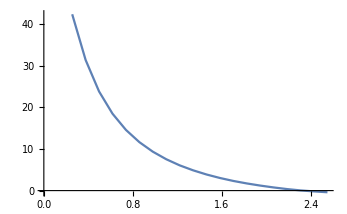

```mathematica
ListLinePlot[Thread[{Rb,A18Beta}]]
```

#### Plotting the chord length

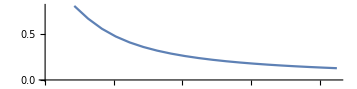

```mathematica
ListLinePlot[Thread[{Rb,A18lengthList}], AspectRatio->.25]
```

## Power Generation

### Common Calculations

#### Averaged Sections

```mathematica
For[i = 1; Rb2 = {}, i < Length[Rb], i++, AppendTo[Rb2, (Rb[[i]] + Rb[[i + 1]]) /2]]
Rb2
```

{0.315395,0.436184,0.556974,0.677763,0.798553,0.919342,1.04013,1.16092,1.28171,1.4025,1.52329,1.64408,1.76487,1.88566,2.00645,2.12724,2.24803,2.36882,2.48961}

#### Speed Ratio for Averaged Sections

```mathematica
λr2 =λd Rb2 / R1
```

{0.660561,0.913542,1.16652,1.4195,1.67248,1.92547,2.17845,2.43143,2.68441,2.93739,3.19037,3.44335,3.69633,3.94931,4.20229,4.45527,4.70826,4.96124,5.21422}

### Airfoil A18

#### Average Length Sections

```mathematica
For[i = 1; A18lengthList2 = {}, i < Length[A18lengthList], i++, AppendTo[A18lengthList2, (A18lengthList[[i]] + A18lengthList[[i + 1]]) /2]]
A18lengthList2
```

{0.731509,0.608055,0.511631,0.437967,0.381172,0.336577,0.300872,0.271755,0.24762,0.227322,0.210035,0.195147,0.1822,0.170841,0.1608,0.151862,0.143856,0.136645,0.130117}

#### Average Pitch Angles

```mathematica
For[i = 1; A18Beta2  = {}, i < Length[A18Beta], i++, AppendTo[A18Beta2 , (A18Beta[[i]] + A18Beta[[i + 1]]) /2]]
A18Beta2
```

{36.841,27.5732,21.1299,16.515,13.0973,10.4861,8.43714,6.79569,5.46436,4.36638,3.44455,2.66797,2.01451,1.45994,0.979185,0.558059,0.201893,-0.0767161,-0.296384}

#### Forces along the blade

```mathematica
A18TFList = Fblade[A18CFT[theta[λr2]-A18Beta2, λr2], Vr[Vw, Vw λr2], A18lengthList2, Δr];
```

```mathematica
A18NFList = Fblade[A18CFN[theta[λr2]-A18Beta2, λr2], Vr[Vw, Vw λr2], A18lengthList2, Δr];
```

```mathematica
A18TF[V_]:=Piecewise[{
{ Total[Fblade[A18CFT[theta[λr2]-A18Beta2, λr2], Vr[V, V λr2], A18lengthList2, Δr] Rb2] / R1,  RPM[V,λd, R1] ≤ rpm1 },

{ Total[Fblade[A18CFT[ArcTan[(60 V)/(3*Rb2 rpm1 π)]/Degree-A18Beta2, (Rb2 rpm1 π)/(30 V)], Vr[V, (Rb2 rpm1 π)/30], A18lengthList2, Δr] Rb2] /R1,  RPM[V,λd, R1] > rpm1 } }];
```

```mathematica
A18NF[V_]:=Piecewise[{
{ Total[Fblade[A18CFN[theta[λr2]-A18Beta2, λr2], Vr[V, V λr2], A18lengthList2, Δr] Rb2] / R1,  RPM[V,λd, R1] ≤ rpm1 },

{ Total[Fblade[A18CFN[ArcTan[(60 V)/(3*Rb2 rpm1 π)]/Degree-A18Beta2, (Rb2 rpm1 π)/(30 V)], Vr[V, (Rb2 rpm1 π)/30], A18lengthList2, Δr] Rb2] /R1,  RPM[V,λd, R1] > rpm1 } }];
```

```mathematica
A18CT[V_]:= (2 A18TF[V])/(δa π V^2 R1^2)
```

#### Out Power

```mathematica
A18Po[V_]:=Piecewise[{
{ (Z1 π)/30 RPM[V, λd, R1] Total[Fblade[A18CFT[theta[λr2]-A18Beta2, λr2], Vr[V, V λr2], A18lengthList2, Δr] Rb2],  RPM[V,λd, R1] ≤ rpm1 },

{ (Z1 π)/30 rpm1 Total[Fblade[A18CFT[ArcTan[(60 V)/(3*Rb2 rpm1 π)]/Degree-A18Beta2, (Rb2 rpm1 π)/(30 V)], Vr[V, (Rb2 rpm1 π)/30], A18lengthList2, Δr] Rb2],  RPM[V,λd, R1] > rpm1 }
}]
```

```mathematica
A18Po[Vw]
```

5937.71

```mathematica
Pw[Vw, R1, 1]
```

12512.3

```mathematica
A18Po[Vw]/Pw[Vw, R1, 1]
```

0.474551

```mathematica
A18Po[15]/Pw[15, R1, 1]
```

InterpolatingFunction::dmval: Input value {19.7118} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {20.0138} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {19.4749} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-1.45062

```mathematica
A18TF[Vw]
A18NF[Vw]
```

37.0595

241.242

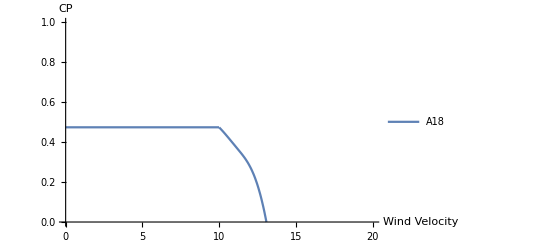

```mathematica
Plot[{A18Po[v]/Pw[v, R1, 1]} ,{v,0,Vw +10}, PlotRange->{0,1},AxesLabel->{"Wind Velocity", "CP"} ,PlotLegends->{"A18"}]
```

### Chart

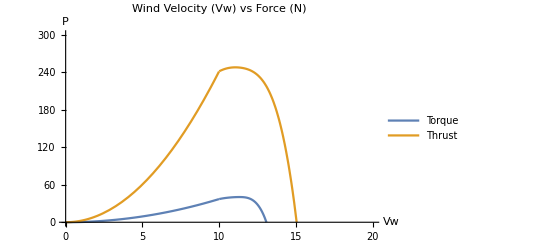

```mathematica
Plot[{A18TF[v], A18NF[v]} ,{v,0,Vw +10}, PlotRange->{0,300},PlotLabel->Style["Wind Velocity (Vw) vs Force (N)", Black,30,FontFamily->"Times New Roman",Italic],AxesLabel->{Style["Vw", Black,20,FontFamily->"Times New Roman"], Style["P", Black,20,FontFamily->"Times New Roman",Italic]} ,PlotLegends->{"Torque","Thrust"}]
```

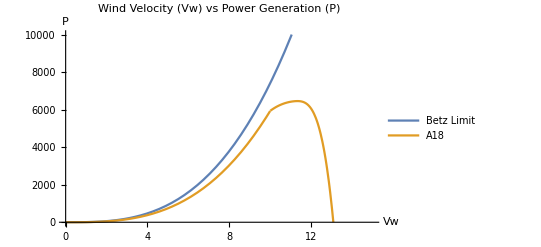

```mathematica
Plot[{Pw[v, R1, CPmax], A18Po[v]} ,{v,0,Vw +5}, PlotRange->{0,10000},PlotLabel->Style["Wind Velocity (Vw) vs Power Generation (P)", Black,30,FontFamily->"Times New Roman",Italic],AxesLabel->{Style["Vw", Black,20,FontFamily->"Times New Roman"], Style["P", Black,20,FontFamily->"Times New Roman",Italic]} ,PlotLegends->{"Betz Limit","A18"}]
```

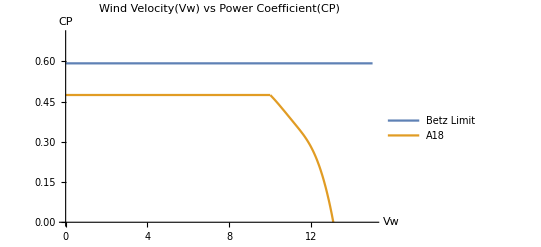

```mathematica
Plot[{Pw[v, R1, CPmax]/Pw[v, R1, 1],A18Po[v]/Pw[v, R1, 1]} ,{v,0,Vw +5}, PlotRange->{0,.7},PlotLabel->Style["Wind Velocity(Vw) vs Power Coefficient(CP)", Black,30,FontFamily->"Times New Roman",Italic],AxesLabel->{Style["Vw", Black,20,FontFamily->"Times New Roman"], Style["CP", Black,20,FontFamily->"Times New Roman",Italic]} ,PlotLegends->{"Betz Limit","A18"}]
```

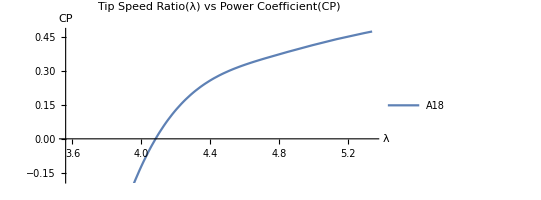

```mathematica
ParametricPlot[{TSRD[v],A18Po[v]/Pw[v, R1, 1]} ,{v,0,Vw +5},PlotLabel->Style["Tip Speed Ratio(λ) vs Power Coefficient(CP)", Black,30,FontFamily->"Times New Roman",Italic],AxesLabel->{Style["λ", Black,20,FontFamily->"Times New Roman"], Style["CP", Black,20,FontFamily->"Times New Roman",Italic]} ,PlotLegends->{"A18"}, AspectRatio->1/2]
```

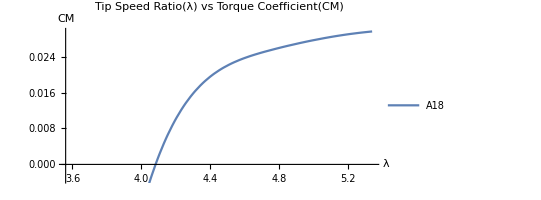

```mathematica
ParametricPlot[{TSRD[v],A18CT[v]} ,{v,0,Vw +5},PlotLabel->Style["Tip Speed Ratio(λ) vs Torque Coefficient(CM)", Black,30,FontFamily->"Times New Roman",Italic],AxesLabel->{Style["λ", Black,20,FontFamily->"Times New Roman"], Style["CM", Black,20,FontFamily->"Times New Roman",Italic]} ,PlotLegends->{"A18"}, AspectRatio->1/2]
```

## Exporting Data

### Design Data

```mathematica
SetDirectory[NotebookDirectory[]]
Export["design_data.xls",Thread[{Rb,A18lengthList,A18Beta }],"XLS"]
```

D:\Jesus Rocha\Documents\github\WTDesigner\A18

design_data.xls

### Generation Data

```mathematica
SetDirectory[NotebookDirectory[]]
Export["force_data.xls",Thread[{Rb2,Fblade[A18CFT[theta[λr2]-A18Beta2, λr2], Vr[Vw, Vw λr2], A18lengthList2, Δr],Fblade[A18CFN[theta[λr2]-A18Beta2, λr2], Vr[Vw, Vw λr2], A18lengthList2, Δr] }],"XLS"]
Export["power_data.xls",Table[{v, A18Po[v]},{v,0,25,1  }],"XLS"]
```

D:\Jesus Rocha\Documents\github\WTDesigner\A18

force_data.xls

InterpolatingFunction::dmval: Input value {13.6124} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {13.6359} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {13.3124} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

power_data.xls

```mathematica
Pw[13.98, R1,0.51696731417262 ]
```

17673.4

```mathematica
A18Po[15]
```

InterpolatingFunction::dmval: Input value {19.7118} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {20.0138} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {19.4749} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-61257.9

```mathematica
Pw[13.97, R1, 1]
```

34113.4